# Coherent Photon Background

```mathematica
path= "C:\\Users\\kimbe\\Dropbox\\CPB"
```

C:\Users\kimbe\Dropbox\CPB

## Constants

```mathematica
Avi=1/(1.66*10^-27) 1/kg;(*inverse of Avogadro's number*)
MNSi=28*10^6;
MNGe=64*10^6;
MNSi=28.0855*10^6;
MNC=12.0107*10^6;
MNGa=69.7*10^6;
MNAs=74.92*10^6;
MNAl=26.98*10^6;
MNO=16.0*10^6;
NTSi=1/(MNSi*10^-6)*Avi;(*number of silicion particles/kg*)
NTGe=1/(MNGe*10^-6)Avi;
NTGaAs=1/((MNGa +MNAs)*10^-6)Avi;(*number of GaAs molecules/kg*)
NTGaAsGa=0.5 NTGaAs;
NTGaAsAs=0.5 NTGaAs;
NTSiC=1/((MNSi+MNC)*10^-6)Avi;
NTSiCSi=0.5 NTSiC;
NTSiCC=0.5 NTSiC;
NTAl2O3=1/((3*MNO+2*MNAl)*10^-6)Avi;(*number of Al3O2 molecules/kg, molar mass = 101.96 g/mol*)
NTAl2O3Al=2/5 NTAl2O3 ;
NTAl2O3O=3/5 NTAl2O3;
```

## Signal GaAs

### from https://arxiv.org/pdf/1910.08092.pdf

```mathematica
hm10={308.2827216089995,1737.5392525289546,2419.695977157717,6971.791769248949,13580.619242210725,7729.9720572130955,1900.6562193793038,635.7649050566099,885.1044848903508,1133.567970047748,1974.5665825479743,2198.6900734407386,1087.7607587013995,1741.904001102644,3688.9981905304817,7187.000940814769,682.8383169040131,10^-8};
hm1={31.126189325639643,54.214833035155294,60.33732187405113,243.15688748201035,338.6201155467752,277.2258951407639,144.91391923877822,144.3589342009516,206.82730591717967,206.82730591717967,358.49652806898854,356.9654945419164,197.56353703766004,454.8833890156425,728.7577532231315,1166.8362795200073,28.967588417689246,10^-8};
hm01={456.02606917122046,1737.7956994253996,988.773537372452,111.13982217781748,0.21049172187989407,0,0,0,0,0,0,0,0,0,0,0.4509065095484821,10^-8};
lm10={26271.902604675663,13400.427210994556,4671.878346444268,2924.837181035148,2601.682149967308,1628.7874214985482,855.4672535565667,619.973150025558,476.39380104013213,423.7587160604046,449.3061600600449,388.1352179939232,176.10136077199263,355.5064279213931,657.3499135734733,1180.412767677829,61.395366074226786,10^-8};
lm1={2601.6821499673106,1288.752413238365,423.7587160604055,209.910372010855,123.94252485211939,79.8991893238432,59.624359780327524,40.75392965871761,29.535136548350142,21.40466694217516,16.447568163493084,7.6841037554689455,2.601682149967303,7.2471873990272115,7.6841037554689455,16.93610584916726,0.9070414181116753,10^-8};
lm01={1.0145991833857213,209.910372010855,65.0967523045815,4.671878346444268,0.12762395627383402,10^-8,0,0,0,0,0,0,0,0,0,0.005568813990945245,0};
tab1=Table[j,{j,0,36,2.0}];
Khm10[ω_]:=Piecewise[Table[{Max[hm10[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];;
Klm10[ω_]:=Piecewise[Table[{Max[lm10[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Khm1[ω_]:=Piecewise[Table[{Max[hm1[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Klm1[ω_]:=Piecewise[Table[{Max[lm1[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Khm01[ω_]:=Piecewise[Table[{Max[hm01[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
Klm01[ω_]:=Piecewise[Table[{Max[lm01[[i]],10^-8],tab1[[i]]<=ω<tab1[[i+1]]},{i,1,Length[tab1]-1}]];
```

### from DarkElf (https://arxiv.org/abs/2104.12786)

```mathematica
SetDirectory[StringJoin[path,"\\DARKELF_GaAs"]];
omegaeV=Import["omega.csv"]//Flatten;
gaas10MeV = Import["gaas10MeV.csv"]//Flatten;
gaas1MeV = Import["gaas1MeV.csv"]//Flatten;
gaas01MeV = Import["gaas1MeV.csv"]//Flatten;
gaas001MeV = Import["gaas10MeV.csv"]//Flatten;
(*For different materials or different masses use DARKELF directly to generate more signals https://github.com/tongylin/DarkELF*)
```

```mathematica
gaas10MeVint=Interpolation[Transpose[{omegaeV,gaas10MeV}]];
gaas1MeVint=Interpolation[Transpose[{omegaeV,gaas1MeV}]];
gaas01MeVint=Interpolation[Transpose[{omegaeV,gaas01MeV}]];
gaas001MeVint=Interpolation[Transpose[{omegaeV,gaas001MeV}]];
```

```mathematica
tab=Table[j,{j,0*10^-3,100.*10^-3,2.0*10^-3}];
DElm10[ω_]:=Piecewise[Table[{Max[NIntegrate[gaas10MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm1[ω_]:=Piecewise[Table[{Max[NIntegrate[gaas1MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm01[ω_]:=Piecewise[Table[{Max[NIntegrate[gaas01MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
DElm002[ω_]=Piecewise[Table[{Max[NIntegrate[gaas002MeVint[x],{x,tab[[i]],tab[[i+1]]}],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]];
```

NIntegrate::inumr: The integrand gaas002MeVint[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.002}}.

NIntegrate::inumr: The integrand gaas002MeVint[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.002,0.004}}.

NIntegrate::inumr: The integrand gaas002MeVint[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.004,0.006}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::nlim: x = {0.,0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018,«41»}⟦i⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

## Loading phonon DOS

```mathematica
(*This section reads in the POS for monoatomic materials Si and Ge and the partial POS for GaAs, SiC, and Subscript[Al, 2] Subscript[O, 3] from various sources in the literature (add documentation). It standardizes the x-axis to be in keV and the overall normalization to be such that ∫ dω f(ω) = 1 for the POS and ∫ dω Subscript[f, 1](ω)+ Subscript[f, 2](ω) = 1 for diatomic materials*)
```

### Monoatomic Materials (Si, Ge)

```mathematica
SetDirectory[StringJoin[path,"\\Phonon_DOS"]];
Siphon=Sort[Import["Si_monoatomic.csv"]];
Siphonx=Siphon[[All,1]]*10^-3; (*convert eV input to keV*)
Siphony=Siphon[[All,2]]; 
Siphonyn=Siphony/NIntegrate[Interpolation[Transpose[{Siphonx,Siphony}],InterpolationOrder-> 1][x],{x,Siphonx[[1]],Siphonx[[-1]]}];(*normalize such that ∫ dω f(ω) = 1*)
SiDOS=Transpose[{Siphonx,Siphonyn}];
Gephon =Import["Ge_monoatomic.csv"];
Gephonx=Gephon[[All,1]]*10^-6; (*convert meV input to keV*)
Gephony=Gephon[[All,2]]; 
Gephonyn=Gephony/NIntegrate[Interpolation[Transpose[{Gephonx,Gephony}],InterpolationOrder-> 1][x],{x,0,Gephonx[[-1]]}];(*normalize such that ∫ dω f(ω) = 1*)
GeDOS=Transpose[{Gephonx,Gephonyn}];
```

### Diatomic Materials (GaAs, SiC, Al_2 O_3)

#### GaAs

```mathematica
SetDirectory[StringJoin[path,"\\Phonon_DOS"]];
GaAsGa=Sort[Import["GaAs_Ga.csv"]];
GaAsAs=Sort[Import["GaAs_As.csv"]];
icmtokeV=1.98*10^-14*10^6;
GaAsGax=GaAsGa[[All,1]]*(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
GaAsGay=GaAsGa[[All,2]];
GaAsAsx=GaAsAs[[All,1]]*(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
GaAsAsy=GaAsAs[[All,2]];
GaAsGayn =GaAsGay/(NIntegrate[Interpolation[Transpose[{GaAsGax,GaAsGay}],InterpolationOrder-> 1][x],{x,GaAsGax[[1]],GaAsGax[[-1]]}]+NIntegrate[Interpolation[Transpose[{GaAsAsx,GaAsAsy}],InterpolationOrder-> 1][x],{x,GaAsAsx[[1]],GaAsAsx[[-1]]}] );(*normalize such that ∫ dω Subscript[f, 1](ω) +Subscript[f, 2](ω) = 1*)
GaAsAsyn =GaAsAsy/(NIntegrate[Interpolation[Transpose[{GaAsGax,GaAsGay}],InterpolationOrder-> 1][x],{x,GaAsGax[[1]],GaAsGax[[-1]]}]+NIntegrate[Interpolation[Transpose[{GaAsAsx,GaAsAsy}],InterpolationOrder-> 1][x],{x,GaAsAsx[[1]],GaAsAsx[[-1]]}] );
GaAsGapDOS=Transpose[{GaAsGax,GaAsGayn}];
GaAsAspDOS=Transpose[{GaAsAsx,GaAsAsyn}];
```

#### SiC

```mathematica
SiCSi=Sort[Import["SiC_Si.csv"]];
SiCC=Sort[Import["SiC_C.csv"]];
SiCSix =  SiCSi[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
SiCSiy = SiCSi[[All,2]];
SiCCx =  SiCC[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
SiCCy = SiCC[[All,2]];
SiCSiyn = SiCSiy/(NIntegrate[Interpolation[Union[Transpose[{SiCSix,SiCSiy}],SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1][x],{x,SiCSix[[1]],SiCSix[[-1]]}]+NIntegrate[Interpolation[Transpose[{SiCCx,SiCCy}],InterpolationOrder-> 1][x],{x,SiCCx[[1]],SiCCx[[-1]]}] );(*normalize such that ∫ dω Subscript[f, 1](ω) +Subscript[f, 2](ω) = 1*)
SiCCyn = SiCCy/(NIntegrate[Interpolation[Union[Transpose[{SiCSix,SiCSiy}],SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1][x],{x,SiCSix[[1]],SiCSix[[-1]]}]+NIntegrate[Interpolation[Transpose[{SiCCx,SiCCy}],InterpolationOrder-> 1][x],{x,SiCCx[[1]],SiCCx[[-1]]}] );
SiCSipDOS=Transpose[{SiCSix,SiCSiyn}];
SiCSipDOS=Union[SiCSipDOS,SameTest->(#1[[1]]==#2[[1]]&)];
SiCCpDOS=Transpose[{SiCCx,SiCCyn}];
```

#### Al_2 O_3

```mathematica
Al2O3Al=Sort[Import["Al3O2_Al.csv"]];
Al2O3O=Sort[Import["Al3O2_O.csv"]];
Al2O3Alx =  Al2O3Al[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
Al2O3Aly = Al2O3Al[[All,2]];
Al2O3Ox =  Al2O3O[[All,1]] *(icmtokeV 2π);(*convert frequency in cm^-1 to energy in keV *)
Al2O3Oy = Al2O3O[[All,2]];
Al2O3Alyn = Al2O3Aly/(NIntegrate[Interpolation[Transpose[{Al2O3Alx,Al2O3Aly}],InterpolationOrder-> 1][x],{x,Al2O3Alx[[1]],Al2O3Alx[[-1]]}]+NIntegrate[Interpolation[Transpose[{Al2O3Ox,Al2O3Oy}],InterpolationOrder-> 1][x],{x,Al2O3Ox[[1]],Al2O3Ox[[-1]]}] );(*normalize such that ∫ dω Subscript[f, 1](ω) +Subscript[f, 2](ω) = 1*)
Al2O3Oyn = Al2O3Oy/(NIntegrate[Interpolation[Transpose[{Al2O3Alx,Al2O3Aly}],InterpolationOrder-> 1][x],{x,Al2O3Alx[[1]],Al2O3Alx[[-1]]}]+NIntegrate[Interpolation[Transpose[{Al2O3Ox,Al2O3Oy}],InterpolationOrder-> 1][x],{x,Al2O3Ox[[1]],Al2O3Ox[[-1]]}] );
Al2O3AlpDOS=Transpose[{Al2O3Alx,Al2O3Alyn}];
Al2O3OpDOS=Transpose[{Al2O3Ox,Al2O3Oyn}];
```

## Loading form factors

```mathematica
(*read in the modified form factor g(q) (q[keV]) which acounts for relativistic corrections. Use the commented out section if you want to use the atomic form factor without relativistic corrections instead*)
```

```mathematica
SetDirectory[StringJoin[path,"\\Form_factors\\modifiedformfactors\\large_q"]];
FqGel=Import["mff_Ge.csv"];
FqSil=Import["mff_Si.csv"];
FqGal=Import["mff_Ga.csv"];
FqAsl=Import["mff_As.csv"];
FqCl=Import["mff_C.csv"];
FqAll=Import["mff_Al.csv"];
FqOl= Import["mff_O.csv"];
SetDirectory[StringJoin[path,"\\Form_factors\\modifiedformfactors\\small_q"]];
FqGes=Import["mff_Ge.csv"];
FqSis=Import["mff_Si.csv"];
FqGas=Import["mff_Ga.csv"];
FqAss=Import["mff_As.csv"];
FqCs=Import["mff_C.csv"];
FqAls=Import["mff_Al.csv"];
FqOs= Import["mff_O.csv"];
FqGe=Join[FqGes,FqGel];
FqSi=Join[FqSis,FqSil];
FqSi=Union[FqSi,SameTest->(#1[[1]]==#2[[1]]&)];(*removes duplicates*)
FqGa=Join[FqGas,FqGal];
FqAs=Join[FqAss,FqAsl];
FqC=Join[FqCs,FqCl];
FqC=Union[FqC,SameTest->(#1[[1]]==#2[[1]]&)];
FqAl=Join[FqAls,FqAll];
FqO=Join[FqOs,FqOl];
```

```mathematica
(*SetDirectory[StringJoin[path,"\\Form_factors\\atomicformfactors\\small_q"]];
FqGes=Import["formfactor_Ge4+.csv"];
FqSis=Import["formfactor_Si4+.csv"];
FqGas=Import["formfactor_Ga.csv"];
FqAss=Import["formfactor_As.csv"];
FqCs=Import["formfactor_C.csv"];
FqAls=Import["formfactor_Al.csv"];
FqOs=Import["formfactor_O.csv"];
SetDirectory[StringJoin[path,"\\Form_factors\\atomicformfactors\\large_q"]];
FqGel=Import["formfactor_Ge4+.csv"];
FqSil=Import["formfactor_Si4+.csv"];
FqGal=Import["formfactor_Ga.csv"];
FqAsl=Import["formfactor_As.csv"];
FqCl=Import["formfactor_C.csv"];
FqAll=Import["formfactor_Al.csv"];
FqOl= Import["formfactor_O.csv"];
FqGe=Join[FqGes,FqGel];
FqSi=Join[FqSis,FqSil];
FqGa=Join[FqGas,FqGal];
FqAs=Join[FqAss,FqAsl];
FqC=Join[FqCs,FqCl];
FqAl=Join[FqAls,FqAll];
FqO=Join[FqOs,FqOl];*)
```

## Differential rate calculation

```mathematica
(*read in the modified form factor g(q) (q[keV]) which acounts for relativistic corrections. Use the commented out section if you want to use the atomic form factor without relativistic corrections instead*)
```

```mathematica
dσdq[pγ_,FF_]:=Module[{pγin=pγ,FFin=FF,α,me,Fq},
α=1/137;
me=0.511*10^3;(*electron mass in keV*)
Fq=Interpolation[Union[FFin,SameTest->(#1[[1]]==#2[[1]]&)],InterpolationOrder-> 1];

(q/pγin^2)(α^2/(2 me^2))(1+(1- q^2/(2 pγin^2))^2)(Fq[q])^2 2π ](*returns dσ/dq(q) where cos(θ) is rewritten as (1-q^2/(2 pγ^2)), and dcosθ/dq = q/pγ^2  *)
```

```mathematica
M2[M_,DOS_]:=Module[{Min=M,DOSin=DOS,ωmax,ωmin,pDOS,DW,T2,T3},
ωmin=DOSin[[All,1]][[1]];
ωmax=DOSin[[All,1]][[-1]];
pDOS[ω_]:=Piecewise[{{Interpolation[DOSin,InterpolationOrder-> 1][ω],ωmin<=ω<ωmax}}];
DW[q_]:=(q^2/(4 Min))NIntegrate[pDOS[ω]/ω,{ω,ωmin,ωmax}];
T2=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))(pDOS[ωp]/ωp),{ωp,ωmin,2ωmax}]},{ω,ωmin,2ωmax,2(ωmax/100)}],InterpolationOrder-> 1];
T3=Interpolation[Table[{ω,NIntegrate[(pDOS[ω-ωp]/(ω-ωp))T2[ωp],{ωp,ωmin,3ωmax}]},{ω,ωmin,3ωmax,3(ωmax/100)}],InterpolationOrder-> 1];
ⅇ^(-2DW[q])((q^2/(2Min))(pDOS[ω]/ω)+(1/Factorial[2])(q^2/(2Min))^2 T2[ω]+(1/Factorial[3])(q^2/(2Min))^3 T3[ω])](*returns S(q,ω) up to n = 3 multiphonon contributions*)
```

```mathematica
Rate[MN_,NT_,DOS_,FF_,γlist_]:=Module[{MNin=MN,DOSin=DOS,γin=γlist,FFin=FF,S,Rin,tab},
S[q_,ω1_]=M2[MNin,DOSin]/.ω-> ω1;
vincmps=3*10^10 cm/s;
spyear=60*60*24*366(s/year);
ikeVtocm=(0.1967*10^-13*10^6 (cm/keV));
Rin[ωmin_,ωmaxx_]:=(kg year NT*vincmps*(spyear)(ikeVtocm)^2*1/cm^3 NIntegrate[Sum[dσdq [γin[[j]][[1]],FFin]*γin[[j]][[2]],{j,1,Length[γin]}]*S[q,ω1],{q,0,300},{ω1,ωmin,ωmaxx},WorkingPrecision-> MachinePrecision,Method->"MonteCarlo"]*keV^2);
tab=Table[j,{j,0*10^-3,0.1*10^-3,0.002*10^-3}];
Piecewise[Table[{Max[Rin[tab[[i]],tab[[i+1]]],10^-8],tab[[i]]<=ω<tab[[i+1]]},{i,1,Length[tab]-1}]]]
```

## Plots

```mathematica
$PlotTheme="Classic";

Clear[fticksR,PrettyExp,fticksRNoLabels,fticksRlinear,fticksRlinearnoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]];
(* Axis for y versus x: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(*Axis for linear ticks*)
fticksRlinear[min_,max_,AMAX_,SUB_]:=Flatten[Table[Prepend[Flatten[Table[{x+i*AMAX/SUB,"",{.008,0}},{i,1,SUB-1}],{1}],{x,x,{.02,0}}],{x,Floor[min],Ceiling[max],AMAX}],1];

fticksRlinearnoLabels[min_,max_,AMAX_,SUB_]:=Flatten[Table[Prepend[Flatten[Table[{x+i*AMAX/SUB,"",{.008,0}},{i,1,SUB-1}],{1}],{x,"",{.02,0}}],{x,Floor[min],Ceiling[max],AMAX}],1];
fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

```mathematica
RGaAs[ω_]=Rate[MNGa,NTGaAsGa,GaAsGapDOS,FqGa,{{1461,1/0.04*4.396833647327371*^-16}}]+Rate[MNAs,NTGaAsAs,GaAsAspDOS,FqAs,{{1461,1/0.04*4.396833647327371*^-16}}];
RGaAsn[ω_]=Rate[MNGa,NTGaAsGa,GaAsGapDOS,FqGa,{{1461,6.85*10^-18},{2614,5.6*10^-18}}]+Rate[MNAs,NTGaAsAs,GaAsAspDOS,FqAs,{{1461,6.85*10^-18},{2614,5.6*10^-18}}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

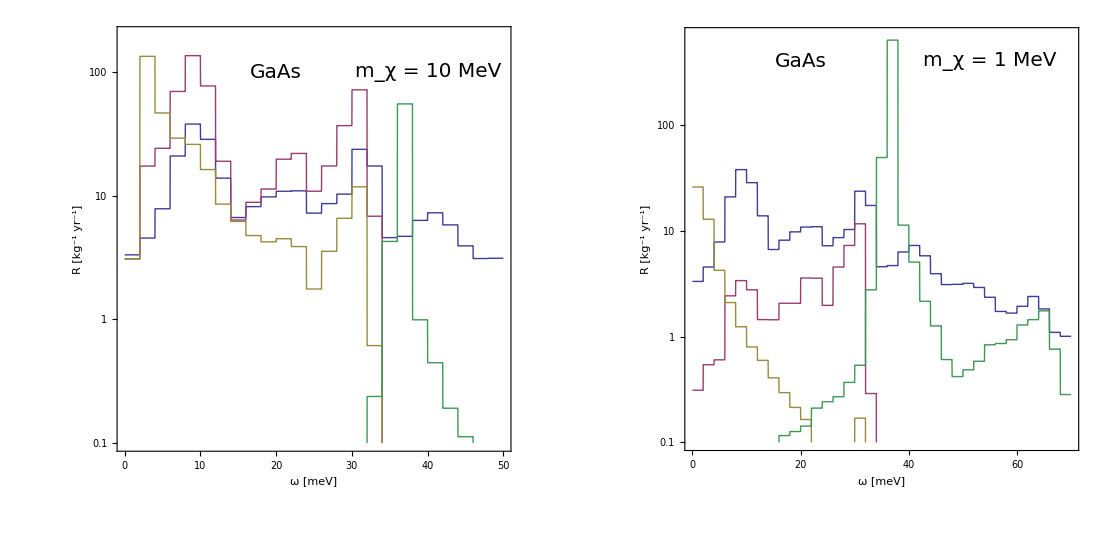

```mathematica
<<MaTeX`

myplot1=LogPlot[{ RGaAs[10^-6 ω],10^-2 Khm10[ω],10^-2 Klm10[ω],DElm10[10^-3 ω]},{ω,0,50},PlotRange->{{0,50},{0.1,200}},Frame->True,FrameTicks->{{fticksR[0.1,100,0],fticksRNoLabels[0.1,100,0]},{fticksRlinear[0,50,10,2],fticksRlinearnoLabels[0,50,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick, Thin,Thin,Thin,Thin},PlotLegends->{ Placed[{MaTeX["\\text{coherent photon background}"],MaTeX["\\text{heavy mediator};\\, \\sigma_{n} = 10^{-45}\, \\text{cm}^2",Magnification-> m3],MaTeX["\\text{light mediator};\\, \\sigma_{n} = 10^{-45}\, \\text{cm}^2",Magnification-> m3],MaTeX["\\text{light dark photon};\\, \\sigma_{e} = 10^{-38}\, \\text{cm}^2",Magnification-> m3] },{{0.34,0.2}}]},Epilog->{ Text[Style["m_χ = 10 MeV",FontSize-> 20,FontFamily->"Times"],{40,Log[100]}],Text[Style["GaAs",FontSize-> 20,FontFamily->"Times"],{20,Log[100]}]}];
myplot2=LogPlot[{ RGaAs[10^-6 ω],10^-2 Khm1[ω],10^-2 Klm1[ω],DElm1[10^-3 ω]},{ω,0,70},PlotRange->{{0,70},{0.1,700}},Frame->True,FrameTicks->{{fticksR[0.1,800,0],fticksRNoLabels[0.1,800,0]},{fticksRlinear[0,70,10,2],fticksRlinearnoLabels[0,70,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick, Thin,Thin,Thin,Thin},Epilog->{ Text[Style["m_χ = 1 MeV",FontSize-> 20,FontFamily->"Times"],{55,Log[400]}],Text[Style["GaAs",FontSize-> 20,FontFamily->"Times"],{20,Log[400]}]}];
GraphicsGrid[{{myplot1,myplot2}},ImageSize-> 1100]
```

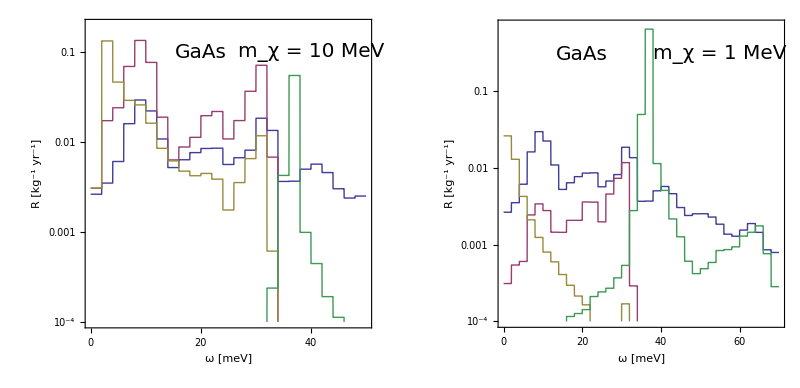

```mathematica
myplot1=LogPlot[{ RGaAsn[10^-6 ω],10^-3 10^-2 Khm10[ω],10^-3 10^-2 Klm10[ω],10^-3 DElm10[10^-3 ω]},{ω,0,50},PlotRange->{{0,50},{10^-4,0.2}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,70,10,2],fticksRlinearnoLabels[0,70,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick, Thin,Thin,Thin,Thin},PlotLegends->{ Placed[{MaTeX["\\text{coherent photon background}"],MaTeX["\\text{heavy mediator};\\, \\sigma_{n} = 10^{-48}\, \\text{cm}^2",Magnification-> m3],MaTeX["\\text{light mediator};\\, \\sigma_{n} = 10^{-48}\, \\text{cm}^2",Magnification-> m3],MaTeX["\\text{light dark photon};\\, \\sigma_{e} = 10^{-41}\, \\text{cm}^2",Magnification-> m3] },{{0.34,0.2}}]},Epilog->{ Text[Style["m_χ = 10 MeV",FontSize-> 20,FontFamily->"Times"],{40,Log[0.10]}],Text[Style["GaAs",FontSize-> 20,FontFamily->"Times"],{20,Log[0.1]}]}];
myplot2=LogPlot[{ RGaAsn[10^-6 ω],10^-3 10^-2 Khm1[ω],10^-3 10^-2 Klm1[ω],10^-3 DElm1[10^-3 ω]},{ω,0,70},PlotRange->{{0,70},{10^-4,0.7}},Frame->True,FrameTicks->{{fticksR[10^-4,800,0],fticksRNoLabels[10^-4,800,0]},{fticksRlinear[0,70,10,2],fticksRlinearnoLabels[0,70,10,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick, Thin,Thin,Thin,Thin},Epilog->{ Text[Style["m_χ = 1 MeV",FontSize-> 20,FontFamily->"Times"],{55,Log[0.3]}],Text[Style["GaAs",FontSize-> 20,FontFamily->"Times"],{20,Log[0.3]}]}];
GraphicsGrid[{{myplot1,myplot2}},ImageSize-> 1100]
```

```mathematica
γtest={{1461,1/0.04*4.396833647327371*^-16}};
RSi[ω_]=Rate[MNSi,NTSi,SiDOS,FqSi,γtest];
RGe[ω_]=Rate[MNGe,NTGe,GeDOS,FqGe,γtest];
RGaAs[ω_]=Rate[MNGa,NTGaAsGa,GaAsGapDOS,FqGa,γtest]+Rate[MNAs,NTGaAsAs,GaAsAspDOS,FqAs,γtest];
RSiC[ω_]=Rate[MNSi,NTSiCSi,SiCSipDOS,FqSi,γtest]+Rate[MNC,NTSiCC,SiCCpDOS,FqC,γtest];
RAl2O3[ω_]=Rate[MNAl,NTAl2O3Al,Al2O3AlpDOS,FqAl,γtest]+Rate[MNO,NTAl2O3O,Al2O3OpDOS,FqO,γtest];
```

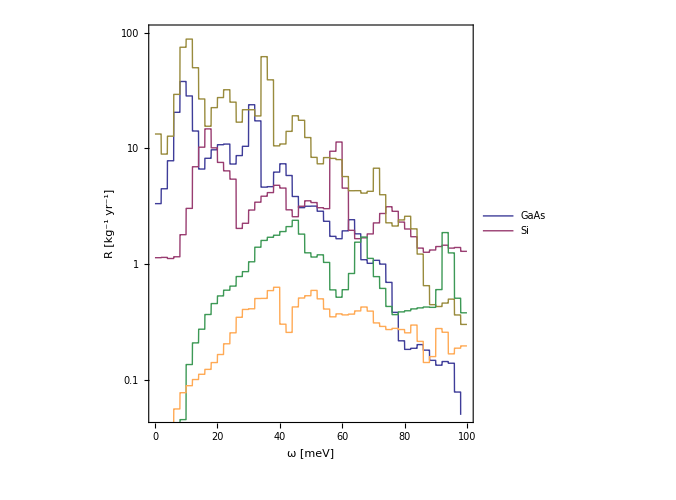

```mathematica
p1=LogPlot[{ RGaAs[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{5*10^-2,100}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, Thick},PlotLegends-> Placed[{"GaAs"},{0.6,0.945}]];
p2=LogPlot[{ 0,RSi[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-2,100}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, Thick},PlotLegends-> Placed[{None,"Si"},{0.56,0.845}]];
p3=LogPlot[{ 0,0,RGe[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-2,100}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, Thick},PlotLegends-> Placed[{None,None,"Ge"},{Right,Top}]];
p4=LogPlot[{0,0,0,RSiC[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-2,100}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, Thick},PlotLegends-> Placed[{None,None,None,"SiC"},{Right,Top}]];
p5=LogPlot[{ 0,0,0,0,RAl2O3[10^-6 ω]},{ω,0,140},PlotRange->{{0,100},{0.5*10^-2,100}},Frame->True,FrameTicks->{{fticksR[10^-4,100,0],fticksRNoLabels[10^-4,100,0]},{fticksRlinear[0,100,20,4],fticksRlinearnoLabels[0,100,20,2]}},FrameLabel->{"ω [meV]","R [kg^-1 yr^-1]"},LabelStyle->21,ImageSize->500,AspectRatio->1,BaseStyle->{FontFamily->"Times"},PlotStyle-> {Thick,Thick, Thick, Thick, {Thick,Lighter[Orange]}},PlotLegends-> Placed[{None,None,None,None,"Al_2O_3"},{Right,Top}]];
Show[p1,p2,p3,p4,p5]
```